# Assembly Dynamics of the Causal Structures : Linear Chains

#### Abhishek Sharma Cronin Lab University of Glasgow

NOTE: Some variable names might be different in the manuscript and Mathematica Notebooks.

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/

## Linear Polymer Dynamics with single monomeric units

#### Assembly of a linear chain with single monomer

In this section, we look into one dimensional assembly space created by linear chains to describe the causation. The depth for an integer is defined by the number of concurrent steps required to create object. Considering a linear chain of structure forming particles, the first order approximation of assembly index can be described as a=log_2(n) and the depth (as the different concurrent processes), d= (⌈log_2(n)⌉). Here, we plot the first order approximation to assembly index of an integer and the depth.

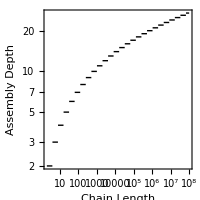

```mathematica
p1=LogLogPlot[Ceiling[Log[2,i]],{i,2,10^8},PlotStyle->{Black,Thick},PlotRange->Full,Frame->True,AspectRatio->1,FrameLabel->{"Chain Length","Assembly Depth"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->200]
```

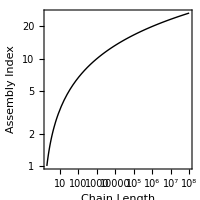

```mathematica
p2=LogLogPlot[Log[2,i],{i,2,10^8},PlotStyle->{Black,Thick},PlotRange->Full,Frame->True,AspectRatio->1,FrameLabel->{"Chain Length","Assembly Index"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->200]
```

```mathematica
Export[baseDirectory<>"AssemblyDepth.png",p1,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyDepth.png

```mathematica
Export[baseDirectory<>"AssemblyDepth.svg",p1]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyDepth.svg

```mathematica
Export[baseDirectory<>"NumberAssembly.png",p2,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/NumberAssembly.png

```mathematica
Export[baseDirectory<>"NumberAssembly.svg",p2]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/NumberAssembly.svg

Here, we generate the complete assembly pool of all the objects up to depth 4. This means the maximum length of the object is given by 2^4=16.

```mathematica
assemblyPool={{1}};poolConnect={};
generatePool[steps_]:=Module[{generateObjects,pos,genObjectsNew},Table[generateObjects=Block[{poolCurrent=Last@assemblyPool,poolTotal=Union@Flatten@assemblyPool},Flatten[Table[{poolCurrent[[i]]->poolCurrent[[i]]+poolTotal[[j]]},{i,Length@poolCurrent},{j,Length@poolTotal}]]];
pos=Partition[Flatten[(Position[generateObjects[[All,2]],#]&/@(Union@Flatten@assemblyPool))],1];
genObjectsNew=If[Length@Flatten@pos!=0,Delete[generateObjects,pos],generateObjects];
poolConnect=Append[poolConnect,genObjectsNew];
assemblyPool= Append[assemblyPool,genObjectsNew[[All,2]]];,{i,steps}]]
```

```mathematica
generatePool[4];
```

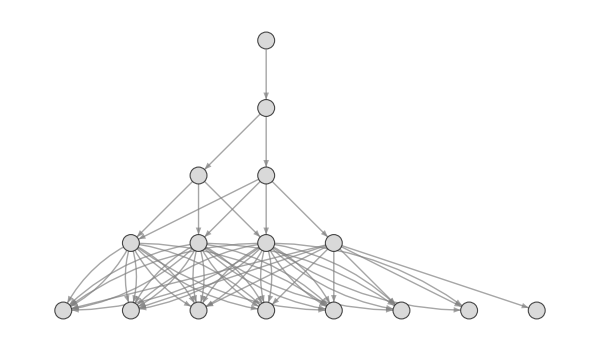

```mathematica
graph=Graph[Flatten[poolConnect],EdgeStyle->Gray,VertexStyle->LightGray,VertexLabels->Placed[Automatic,Center],VertexSize->0.25,ImageSize->600,Epilog->Inset[p2,{1.75,2.5}]]
```

```mathematica
Export[baseDirectory<>"NumberGraph.png",graph,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/NumberGraph.png

```mathematica
Export[baseDirectory<>"NumberGraph.svg",graph]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/NumberGraph.svg

#### Random Growth Model of Linear Sequences

Considering a pure random coupling between linear chains which defines the assembly pool, without any constraints on the population/copy number, the growth of the assembly process could be defined by combining randomly the sequences from the assembly pool which consists of the unique set of all the sequences. It is important to note that this process occurs in assembly space, not in the real physical space. Random Growth Model describes the random discovery of unique objects based on the combination of objects present in the assembly pool. The Random Growth Model in the assembly space is a physical-equivalent process in assembly space but each combination step is not a shortest path and hence the assembly index of the emerging structures needs to be evaluated later.

```mathematica
SeedRandom[110]
```

RandomGeneratorState[…]

```mathematica
(* This step will take some time *)
assemblyPool={1}; (* Consists of unique linear sequences with unique sequences *)
assemblyGen = {1}; (* Generated sequences *)
Block[{newSeq},Monitor[Table[newSeq=Total@RandomChoice[assemblyPool,2];assemblyGen=Append[assemblyGen,newSeq];assemblyPool=Union@assemblyGen,{i,2.5 10^4}],i];];
```

As shown before, the assembly index of the linear chain can be approximated by a=log_2(n) as a first order approximation.

```mathematica
Dimensions/@{assemblyGen,assemblyPool}
```

{{25001},{22874}}

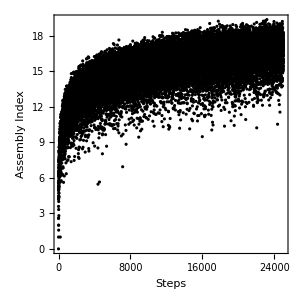

```mathematica
f1=ListPlot[Log[2,assemblyGen],PlotStyle->{Black,PointSize[0.0075]},AspectRatio->1,Frame->True,FrameLabel->{"Steps","Assembly Index"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

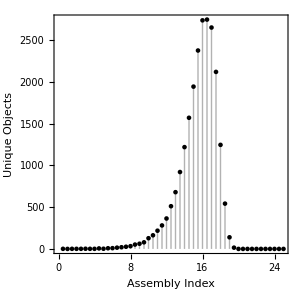

```mathematica
f2=ListPlot[MapThread[{#1,#2}&,{Range[0.5,25,0.5],BinCounts[N@Log2[assemblyPool],{0,25,0.5}]}],Filling->Axis,PlotRange->Full,PlotStyle->Black,FrameLabel->{"Assembly Index","Unique Objects"},Frame->True,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

```mathematica
Export[baseDirectory<>"AssemblyIndex_forwardExample.png",f1,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyIndex_forwardExample.png

```mathematica
Export[baseDirectory<>"AssemblyIndex_forwardExample.svg",f1]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyIndex_forwardExample.svg

```mathematica
Export[baseDirectory<>"AssemblyIndex_Dist.png",f2,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyIndex_Dist.png

```mathematica
Export[baseDirectory<>"AssemblyIndex_Dist.svg",f2]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyIndex_Dist.svg

Considering a process, which is capable of filtering the sequence lengths among the assembly pool, such that for the next step only a subset of the chains in the assembly pool are used for further growth defined by the selection coefficient. Again, this is important to note that this process is about discovery of unique and higher objects. They don’t include real polymerization kinetics.

```mathematica
linearGrowth[n_]:=Module[{assemblyPool,pool,assemblyGen,len},
assemblyPool={1}; (* Consists of unique linear sequences with unique sequences *);
assemblyGen = {1}; (* Generated sequences *)
Block[{newSeq},Monitor[Table[
len=Length@assemblyPool;
pool=assemblyPool[[Ceiling[len(1-n)];;len]]; If[Length@pool!=0,newSeq=Total@RandomChoice[pool,2];assemblyGen=Append[assemblyGen,newSeq];assemblyPool=Union@assemblyGen],{i,5 10^4}],i];];
Return[{assemblyGen,assemblyPool}]]
```

```mathematica
out1=linearGrowth[0.0001];
```

```mathematica
out2=linearGrowth[0.001];
```

```mathematica
out3=linearGrowth[0.01];
```

```mathematica
out4=linearGrowth[0.1];
```

```mathematica
out5=linearGrowth[0.2];
```

```mathematica
out6=linearGrowth[0.4];
```

```mathematica
out7=linearGrowth[0.6];
```

```mathematica
out8=linearGrowth[0.8];
```

```mathematica
Length/@{out1[[1]],out2[[1]],out3[[1]],out4[[1]],out5[[1]],out6[[1]],out7[[1]],out8[[1]]}
```

{50001,50001,50001,50001,50001,50001,50001,50001}

Again approximating the assembly index by a=log_2(n). Here, δ represents the “selection coefficient” which defines the fraction of the subset to be used for combining objects. Plotting the actual trajectory defined by assembly generated (note that this is different from assembly pool). Assembly pool consists only of the list of unique objects. In the assembly generated, a single object can exist more than once.

```mathematica
p4=ListPlot[{Log[2,out1[[1]]],Log[2,out2[[1]]],Log[2,out3[[1]]],Log[2,out4[[1]]],Log[2,out5[[1]]],Log[2,out6[[1]]],Log[2,out7[[1]]],Log[2,out8[[1]]]},ScalingFunctions->{"Log","Log"},PlotRange->Full,PlotStyle->{{Pink,PointSize[0.01]},{Orange,PointSize[0.01]},{Red,PointSize[0.01]},{Magenta,PointSize[0.01]},{Blue,PointSize[0.01]},{Green,PointSize[0.01]},{Brown,PointSize[0.01]},{Black,PointSize[0.01]}},PlotLegends->Placed[LineLegend[{"10^-4","10^-3","10^-2","0.1","0.2","0.4","0.6","0.8"},Spacings->0.1,LegendLabel->"δ"],{0.15,0.65}],AspectRatio->1,Frame->True,FrameLabel->{"Steps","Assembly Index"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

-Graphics-

```mathematica
Export[baseDirectory<>"AssemblyIndex_Selection.png",p4,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyIndex_Selection.png

```mathematica
Export[baseDirectory<>"AssemblyIndex_Selection.svg",p4]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyIndex_Selection.svg

```mathematica
Total@BinCounts[N@Log2[out8[[2]]],{0,200}]
```

49420

```mathematica
Log[2,Max@out1[[2]]]//N
```

29361.7

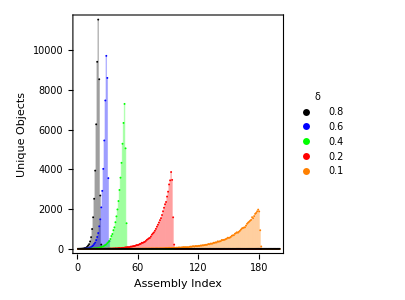

```mathematica
p5=ListPlot[{
MapThread[{#1,#2}&,{Range[200],BinCounts[N@Log2[out8[[2]]],{0,200}]}],MapThread[{#1,#2}&,{Range[200],BinCounts[N@Log2[out7[[2]]],{0,200}]}],
MapThread[{#1,#2}&,{Range[200],BinCounts[N@Log2[out6[[2]]],{0,200}]}],MapThread[{#1,#2}&,{Range[200],BinCounts[N@Log2[out5[[2]]],{0,200}]}],MapThread[{#1,#2}&,{Range[200],BinCounts[N@Log2[out4[[2]]],{0,200}]}],MapThread[{#1,#2}&,{Range[200],BinCounts[N@Log2[out3[[2]]],{0,200}]}]},
PlotLegends->Placed[LineLegend[{"0.8","0.6","0.4","0.2","0.1"},Spacings->0.1,LegendLabel->"δ"],{0.85,0.75}],
Filling->Axis,PlotRange->Full,PlotStyle->{Black,Blue,Green,Red,Orange},FrameLabel->{"Assembly Index","Unique Objects"},
AspectRatio->1,Frame->True,FrameLabel->{"Steps","Assembly Index"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

```mathematica
Export[baseDirectory<>"AssemblyIndex_Selection2.png",p5,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyIndex_Selection2.png

```mathematica
Export[baseDirectory<>"AssemblyIndex_Selection2.svg",p5]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyIndex_Selection2.svg

```mathematica
{Length/@{out1[[1]],out1[[2]]},Total@BinCounts[N@Log2[out1[[2]]],{0,3 10^4}]}
```

{{50001,45997},45997}

```mathematica
{Length/@{out2[[1]],out2[[2]]},Total@BinCounts[N@Log2[out2[[2]]],{0,3 10^4}]}
```

{{50001,48092},48092}

```mathematica
{Length/@{out3[[1]],out3[[2]]},Total@BinCounts[N@Log2[out3[[2]]],{0,3 10^4}]}
```

{{50001,49647},49647}

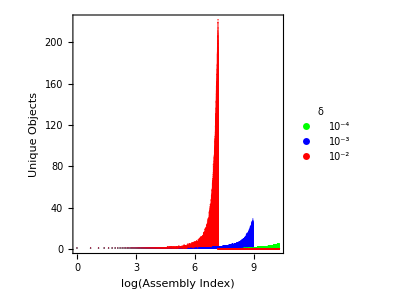

```mathematica
p6=ListPlot[{
MapThread[{Log[#1],#2}&,{Range[3 10^4],BinCounts[N@Log2[out1[[2]]],{0,3 10^4}]}],MapThread[{Log[#1],#2}&,{Range[3 10^4],BinCounts[N@Log2[out2[[2]]],{0,3 10^4}]}],
MapThread[{Log[#1],#2}&,{Range[3 10^4],BinCounts[N@Log2[out3[[2]]],{0,3 10^4}]}]},PlotLegends->Placed[LineLegend[{"10^-4","10^-3","10^-2"},Spacings->0.1,LegendLabel->"δ"],{0.15,0.75}],
Filling->Axis,PlotRange->Full,PlotStyle->{Green,Blue,Red},FrameLabel->{"log(Assembly Index)","Unique Objects"},
AspectRatio->1,Frame->True,FrameLabel->{"Steps","Assembly Index"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},ImageSize->300]
```

```mathematica
Export[baseDirectory<>"AssemblyIndex_Selection3.png",p6,ImageResolution->300]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyIndex_Selection3.png

```mathematica
Export[baseDirectory<>"AssemblyIndex_Selection3.svg",p6]
```

/Users/abhisheksharma/Documents/Projects/Assembly_Theory/Assembly_Theory_Notebooks/AssemblyIndex_Selection3.svg

As and example, here we can show the growth process :

```mathematica
linearGrowth[n_,steps_]:=Module[{assemblyPool,pool,assemblyGen,len},
assemblyPool={1}; (* Consists of unique linear sequences with unique sequences *);
assemblyGen = {1}; (* Generated sequences *)
Block[{newSeq},Monitor[Table[
len=Length@assemblyPool;
pool=assemblyPool[[Ceiling[len(1-n)];;len]]; If[Length@pool!=0,newSeq=Total@RandomChoice[pool,2];assemblyGen=Append[assemblyGen,newSeq];assemblyPool=Union@assemblyGen;
Print["Step : ",i];
Print["Current Assembly Generated: ",assemblyGen];
Print["Current Assembly Pool: ",assemblyPool]],{i,steps}],i];];
Return[{assemblyGen,assemblyPool}]];
```

```mathematica
linearGrowth[0.5,10]
```

Step : 1

Current Assembly Generated: {1,2}

Current Assembly Pool: {1,2}

Step : 2

Current Assembly Generated: {1,2,3}

Current Assembly Pool: {1,2,3}

Step : 3

Current Assembly Generated: {1,2,3,5}

Current Assembly Pool: {1,2,3,5}

Step : 4

Current Assembly Generated: {1,2,3,5,10}

Current Assembly Pool: {1,2,3,5,10}

Step : 5

Current Assembly Generated: {1,2,3,5,10,13}

Current Assembly Pool: {1,2,3,5,10,13}

Step : 6

Current Assembly Generated: {1,2,3,5,10,13,8}

Current Assembly Pool: {1,2,3,5,8,10,13}

Step : 7

Current Assembly Generated: {1,2,3,5,10,13,8,10}

Current Assembly Pool: {1,2,3,5,8,10,13}

Step : 8

Current Assembly Generated: {1,2,3,5,10,13,8,10,26}

Current Assembly Pool: {1,2,3,5,8,10,13,26}

Step : 9

Current Assembly Generated: {1,2,3,5,10,13,8,10,26,13}

Current Assembly Pool: {1,2,3,5,8,10,13,26}

Step : 10

Current Assembly Generated: {1,2,3,5,10,13,8,10,26,13,18}

Current Assembly Pool: {1,2,3,5,8,10,13,18,26}

{{1,2,3,5,10,13,8,10,26,13,18},{1,2,3,5,8,10,13,18,26}}